```mathematica
data =Import["C:\\Users\\Juhász Nóra\\Documents\\GitHub\\ABM-PDE\\StochasticVariability\\theo_results\\theo20.txt", "Table"];
```

dataLength will be 1000, this was just an experiment

```mathematica
dataLength=1000;
```

```mathematica
cleanData={};
```

```mathematica
For[i=1,i<=dataLength, i++,cleanData=Append[cleanData,data[[i]][[4]]]]
```

```mathematica
cleanData;
```

```mathematica
probabilityData={};
```

```mathematica
For[i=0,i<=Max[cleanData], i++,probabilityData=Append[probabilityData,{i,0}]]
```

```mathematica
probabilityData;
```

```mathematica
For[i=1,i<=dataLength, i++,probabilityData[[cleanData[[i]]+1,2]]=probabilityData[[cleanData[[i]]+1,2]] + 1]
```

```mathematica
probabilityData
```

{{0,493},{1,276},{2,113},{3,62},{4,35},{5,12},{6,5},{7,3},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,1}}

```mathematica
N[Sum[probabilityData[[i,1]]*probabilityData[[i,2]]/1000,{i,1,Length[probabilityData]}]]
```

0.956

```mathematica
probDensFunc[x_]:=N[probabilityData[[x+1,2]]/dataLength]
```

```mathematica
probDensFunc[0]
```

0.493

http://math.bme.hu/~nandori/Virtual_lab/stat/expect/Generating.pdf

```mathematica
probGenFunc[z_]:=Sum[probDensFunc[n]*(z^n),{n,0,Max[cleanData]}]
```

```mathematica
probGenFunc[0.01]
```

0.495771

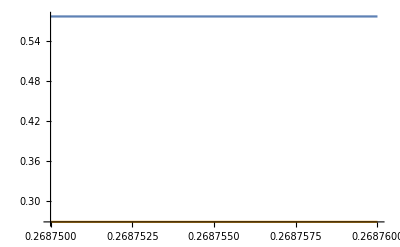

```mathematica
Plot[{probGenFunc[t],t},{t,0.26875,0.26876}]
```

```mathematica
probGenFunc[0.2687]
```

0.576724